```mathematica
Generates simple random circles in the box and writes the list in grain.txt file.
Taken from: http://mathematica.stackexchange.com/questions/84991/plotting-random-circles-in-a-square
```

19

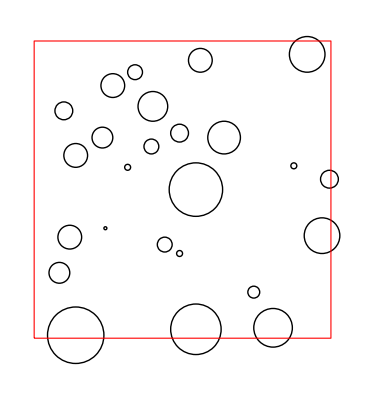

```mathematica
SeedRandom[371]; box =200; num =25; radius=19
f := {RandomInteger[{0,box},2],RandomInteger[{0,radius}]}
l = {f};
While[
Length@l < num,
While[k=f;
Not[And @@ ((# + k)[[2]] < EuclideanDistance[#[[1]],k[[1]]] & /@ l)]];
AppendTo[l,k]];
Graphics[{Circle @@@ l, FaceForm[Transparent],EdgeForm[Red],
Polygon[{{0,0},{0,box},{box,box},{box,0},{0,0}}]}]
```

```mathematica
l[[All,{1,2}]] = l[[All,{2,1}]];
Export["grains.txt",Partition[Flatten[l],3],"TSV"]
```

grains.txt

```mathematica
Flatten[l]
```

{19,28,2,4,148,31,6,98,138,5,88,63,12,184,191,8,53,170,2,175,116,6,199,107,1,48,74,7,46,135,10,80,156,12,194,69,8,112,187,8,24,68,6,20,153,17,109,6,5,68,179,8,28,123,18,109,100,11,128,135,7,17,44,2,63,115,13,161,7,2,98,57,5,79,129}